```mathematica
data=Flatten@Import["C:\\Users\\Sebastian\\Dropbox\\Studie\\Kurser\\Datalogi\\PCSD\\Assignments\\1\\tex\\lots-of-clients_100reqs_zipf0.5.txt","TSV"];
```

```mathematica
fancyData=Nest[
Module[{
nums=TakeWhile[#[[1,2;;]],IntegerQ]
},{
#[[1,(2+Length@nums);;]],
Append[#[[2]],nums]
}]&,{data,{}},25][[2]];
```

```mathematica
latencyData={Length[#],Total[#]/(100*Length[#])}&/@fancyData//N
```

{{1.,6.91},{2.,5.885},{3.,5.17333},{4.,29.315},{5.,21.888},{6.,26.7267},{7.,30.7786},{8.,33.7},{9.,34.9522},{10.,40.047},{11.,43.7},{12.,33.0583},{13.,54.8585},{14.,46.075},{15.,38.3867},{16.,52.0406},{17.,47.8053},{18.,47.9261},{19.,45.2768},{20.,102.153},{21.,94.8105},{22.,86.085},{23.,106.521},{24.,101.57},{25.,109.007}}

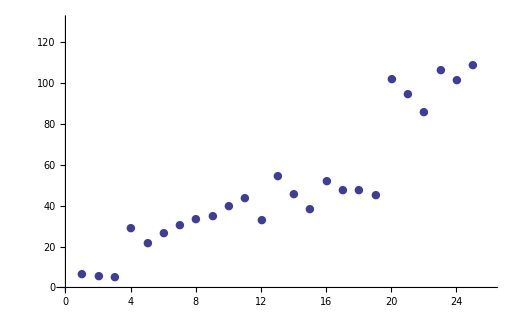

```mathematica
ListPlot[latencyData,PlotRange->{{0,26},{0,130}},PlotMarkers->{Automatic,Small}]
```

```mathematica
throughputData={Length[#],(100*Length[#])/(Total[#]/1000)}&/@fancyData//N
```

{{1.,144.718},{2.,169.924},{3.,193.299},{4.,34.1122},{5.,45.6871},{6.,37.4158},{7.,32.4901},{8.,29.6736},{9.,28.6105},{10.,24.9707},{11.,22.8833},{12.,30.2496},{13.,18.2287},{14.,21.7037},{15.,26.0507},{16.,19.2158},{17.,20.9182},{18.,20.8655},{19.,22.0863},{20.,9.78924},{21.,10.5474},{22.,11.6164},{23.,9.38779},{24.,9.84543},{25.,9.17371}}

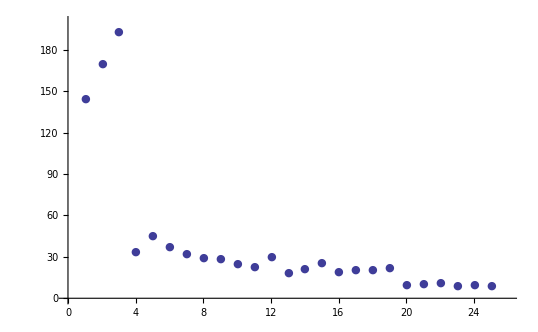

```mathematica
ListPlot[throughputData,PlotRange->{{0,26},{0,200}},PlotMarkers->{Automatic,Small}]
```